```mathematica
selectGraph["DST"][g_,src_]:=Module[{el,gth,gkeys,selkeys,selPos},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
selkeys=Intersection[src,gkeys];
selPos=Flatten[Map[Position[gkeys,#]&,selkeys]];
Graph[Flatten[gth[[selPos]]]]
]
```

```mathematica
selectGraphPara["DST"][g_,src_]:=Module[{el,gth,gkeys,selkeys,selPos},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
selkeys=Intersection[src,gkeys];
selPos=Flatten[ParallelMap[Position[gkeys,#]&,selkeys]];
Graph[Flatten[gth[[selPos]]]]
]
```

```mathematica
selectGraphAs["DST"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
as=Inner[Rule,gkeys,gth,Association];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

```mathematica
selectGraphAs["SRC"][g_,src_]:=Module[{el,gth,gkeys,as},
el=EdgeList[g];
gth=GatherBy[el,#[[1]]&];
gkeys=Map[#[[1,1]]&,gth];
as=Inner[Rule,gkeys,gth,Association];
DeleteCases[Flatten[Map[as[#]&,src]],_Missing]//Graph
]
```

```mathematica
selectEdge["DST"][el_,src_]:=Module[{gth,gkeys,selkeys,selPos},
gth=GatherBy[el,#[[2]]&];
gkeys=Map[#[[1,2]]&,gth];
selkeys=Intersection[src,gkeys];
selPos=Map[Position[gkeys,#]&,selkeys]//Flatten;
Flatten[gth[[selPos]]]//Graph
]
```

```mathematica
selectEdge["SRC"][el_,src_]:=Module[{gth,gkeys,selkeys,selPos},
gth=GatherBy[el,#[[1]]&];
gkeys=Map[#[[1,1]]&,gth];
selkeys=Intersection[src,gkeys];
selPos=Map[Position[gkeys,#]&,selkeys]//Flatten;
Flatten[gth[[selPos]]]//Graph
]
```

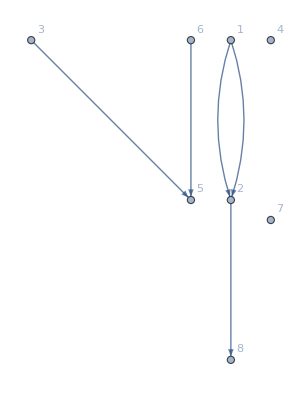

```mathematica
g=Graph[{1,2,3,4,5,6,7,8},{1->2,1->2,3->5,6->5,2->8},VertexLabels->Automatic]
```

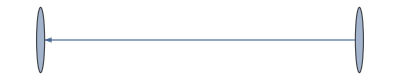

```mathematica
g1=selectGraphAs["SRC"][g,{2,5}]
```

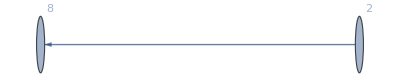

```mathematica
Graph[g1,VertexLabels->Automatic]
```

```mathematica
g2=selectGraphAs["DST"][g,{2,5}]
```

-Graphics-

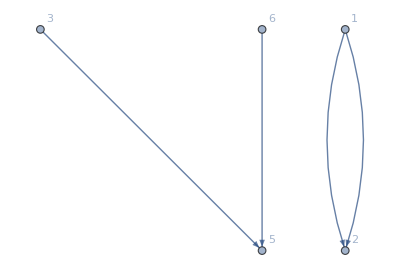

```mathematica
Graph[g2,VertexLabels->Automatic]
```

```mathematica
Subgraph[g,{DirectedEdge[_,5],DirectedEdge[_,2]}]
```

-Graphics-